# 1D FEM Computation

Tiago Amorim

```mathematica
ClearAll;
```

### Options

```mathematica
nPointsPerElem=7; (* Points per element in FEM solution plot*)
nPointsErrorIntPerElem = 11; (* Points per element in error integration*)
nPointsCorrel = 3; (* Number of (h,Error) pairs that define correlation. Uses the values with smaller h in list.*)
bigNumber = 10^12;
Off[LinearSolve::luc];
Off[General::munfl];
```

### Problem Type: a0(x) u’’ + a1(x) u +a2(x) u = f(x), for all 0<=x<=h alfa0 u’(0) + beta0 u(0) = gamma0 alfa1 u’(h) + beta1 u(h) = gamma1

```mathematica
h=8;

a0 = -1; (* not implemented yet*)
a1 = 0.; (* not implemented yet*)
a2 = 0.; (* implemented for constant values only*)

alfa0 = 0.; (* not implemented yet*)
alfa1 = 0.; (* not implemented yet*)
beta0 = 1.; (* initial implementation*)
beta1 = 1.; (* initial implementation*)
gamma0=0.; (* initial implementation*)
gamma1=0.; (* initial implementation*)
```

## Defined Functions

### Initialization

```mathematica
preSolve1DFEM[defineExact_, functionG_, NumberElements_, ExtremeElementsOrder_, InternalElementsOrder_, SameSize_, ElementSizes_]:=Block[{fRight, fx,n, x,y, Nodes, ElemNodes,ElemOrders, Sizes},
If[Not[Length[ElementSizes]==NumberElements] && Not[SameSize],
Print["Enter an appropriate number of element sizes. Review data!"];
];
Sizes = ElementSizes;
(*Will append values if ElementSizes is too small*)
While[Length[Sizes]<NumberElements,
AppendTo[Sizes,Min[Sizes]];
];
Sizes = Accumulate[Sizes]/ Total[Sizes]*h;
fx[x]:=gamma0/beta0-g[0] + x*(gamma1/beta1-gamma0/beta0-g[h]+g[0]);
fRight=If[defineExact, a0*D[functionG[x]+fx[x],x,x]+a1*D[functionG[x]+fx[x],x]+a2*(functionG[x]+fx[x])/.y->x, functionG[x]];
n = NumberElements;
Nodes = N[Table[If[SameSize,{i/n*h,0},{Sizes[[i]],0}],{i,0,n}]];
Nodes[[1]][[1]]=0;
ElemNodes = Table[{i,i+1},{i,1,n}];
ElemOrders = Table[InternalElementsOrder,{i,1,n}];
ElemOrders[[1]] = ExtremeElementsOrder;
ElemOrders[[n]] = ExtremeElementsOrder;
{Nodes, ElemNodes, ElemOrders,fRight}
]
```

```mathematica
SolveExact[defineExact_, g_, verbose_]:=Block[{U,u, x,y,f,fRight,Uexact, dUexact},
f[x]:=gamma0/beta0-g[0] + x*(gamma1/beta1-gamma0/beta0-g[h]+g[0]);
Uexact=If[defineExact, Simplify[g[x]+f[x]],
U[x] /. First @  DSolve[{a0*U''[x]+a1*U'[x]+a2*U[x]==g[x],alfa0*U'[0]+beta0*U[0]==gamma0, alfa1*U'[h]+beta1*U[h]==gamma1},U[x],{x,0,h}]];
dUexact=D[Uexact,x];
fRight:=If[defineExact,
a0*D[g[x]+f[x],x,x]+a1*D[g[x]+f[x],x]+a2*(g[x]+f[x]),
g[x]];
If[verbose,
Print["Problem:"];
Print["  ",TraditionalForm[a0*u''+a1*u'+a2*u ],"=",Simplify[fRight]];
Print["  ",TraditionalForm[alfa0*u'[0]+beta0*u[0]],"=",gamma0];Print["  ",TraditionalForm[alfa1*u'[h]+beta1*u[h]],"=",gamma1];
Print["Exact Solution: ",TraditionalForm[Simplify[Uexact[x]]]];
Print[Plot[Uexact,{x,0,h},PlotRange->All, PlotLabel->"Exact Solution",AxesLabel->{"x","u[x]"}]];
Print["First Derivative: ",TraditionalForm[Simplify[dUexact]]];
Print[Plot[dUexact,{x,0,h},PlotRange->All, PlotLabel->"First Derivative",AxesLabel->{"x","u'[x]"}]];
Print["Right-side Function: ",TraditionalForm[Simplify[fRight]]];
Print[Plot[fRight/.x->y,{y,0,h},PlotRange->All, PlotLabel->"Right-side Function",AxesLabel->{"x","f[x]"}]];
];
{Uexact, dUexact,fRight}
]
```

### Numerical Integration

```mathematica
<<NumericalDifferentialEquationAnalysis`;
GetRule[n_] := GaussianQuadratureWeights[n,-1,1]//Transpose
```

### Master element shape functions

```mathematica
phimaster={(1-ksi)/2,(1+ksi)/2,1-ksi^2};
For[order=3,order<=10,order++,AppendTo[phimaster,phimaster[[-1]]ksi]]
dphimaster=D[phimaster,ksi];
```

### Solve FEM

```mathematica
Solve1DFEM[fRight_, Nodes_,ElemNodes_,ElemOrders_,nPointsPerElem_, uex_, duex_,nPointsErrorIntPerElem_,debug_]:=Block[{ElemEquations, NEquations,XShape,X, ksi, GradX, Jac, elMat, elF,  GlobMat, GlobF, el, StiffEl,nel, Sol, values, dvalues,GlobalError},

(*Element Data*)
ElemEquations=ElemNodes;
NEquations=Length[Nodes]+1;
For[el=1,el<=Length[ElemNodes],el++,
For[order=2,order<=ElemOrders[[el]],order++,
AppendTo[ElemEquations[[el]],NEquations++]]
];
NEquations--;

(*Element Geometry*)
XShape={(1-ksi)/2,(1+ksi)/2};
X[el_]:=Block[{x1,x2,val},
x1=Nodes[[ElemNodes[[el,1]]]];
x2=Nodes[[ElemNodes[[el,2]]]];
val=XShape[[1]]x1+XShape[[2]]x2;
val
];
GradX[el_]:=Block[{},
Grad[X[el],{ksi}]
];
Jac[el_]:=Norm[GradX[el]];

(*Integration of element stiffness*)
Stiff[el_]:=Block[{element,r,np,ord,nfunc,elmat,elf,ip,loc,w,phiel,dphiel,jac,dphielx,xp},
element=el;
ord=ElemOrders[[element]];
np=ord+2;
r=GetRule[np];
nfunc=ord+1;
elmat=Table[0,{nfunc},{nfunc}];
elf=Table[0,{nfunc}];
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
phiel=phimaster[[1;;nfunc]]/.ksi->loc;
dphiel=dphimaster[[1;;nfunc]]/.ksi->loc;
jac=Jac[element]/.ksi->loc;
dphielx=dphiel/jac;
xp=X[element]/.ksi->loc;
elmat+=Table[(-a0*dphielx[[i]]*dphielx[[j]]+a1*phiel[[i]]*dphielx[[j]]+a2*phiel[[i]]*phiel[[j]])w jac,{i,nfunc},{j,nfunc}];
elf+=Table[(fRight/.x->xp[[1]]) phiel[[i]]w jac,{i,nfunc}];
If[debug,
Print["El.",element," ksi=",loc," x=",xp[[1]]," f(x)=",fRight/.x->xp[[1]]];
];
];
{elmat//Simplify,elf//Simplify}
];

(*Assembly Function*)
Assemble[glob_,el_]:=Block[{elst,GMat,GF,eleq,neq,elmat,elf,i,gi,gj,j},
(*elst=Stiff[el];*)
eleq=ElemEquations[[el]];
neq=Length[eleq];
{elmat,elf}=Stiff[el];
If[debug,
Print["Element ",el,": ",MatrixForm[elmat],MatrixForm[elf]];
];
{GMat,GF}=glob;
For[i=1,i<=neq,i++,
gi=eleq[[i]];
GF[[gi]]+=elf[[i]];
For[j=1,j<=neq,j++,
gj=eleq[[j]];
GMat[[gi,gj]]+=elmat[[i,j]]
]
];
{GMat,GF}
];

(*Global Matrices*)
GlobMat=Table[0,{NEquations},{NEquations}];
GlobF=Table[0,{NEquations}];

If[debug,
Print["f(x)=",TraditionalForm[Simplify[fRight]]];
];
For[el=1,el<=Length[ElemEquations],el++,
{GlobMat,GlobF}=Assemble[{GlobMat,GlobF},el]
];

(*Applying Boundary Conditions*)
GlobMat[[1,1]]+= bigNumber * beta0;
GlobF[[1]]+= bigNumber * gamma0;
nel=Length[ElemEquations];
GlobMat[[nel+1,nel+1]]+= bigNumber * beta1;
GlobF[[nel+1]]+= bigNumber * gamma1;

Sol=LinearSolve[GlobMat,GlobF];

GenerateApproximateSolution[ nPtsPerElem_] := Block[{Allval, dAllval, nels, iel,ElementValues,dElementValues},
ElementValues[el_]:=Block[{element,eleq,nfunc,elcoef,elsol,elx,elval},
element=el;
eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}];
elx=X[element];
elval=Table[{elx[[1]],elsol},{ksi,-1,1,2/(nPtsPerElem-1)}]
];
dElementValues[el_]:=Block[{element,eleq,nfunc,elcoef,elsol,elx,elval,jac},
element=el;
eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];
jac=Jac[element];
elsol=Sum[dphimaster[[i]]/jac elcoef[[i]],{i,nfunc}];
elx=X[element];
elval=Table[{elx[[1]],elsol},{ksi,-1,1,2/(nPtsPerElem-1)}]
];

Allval={};
nels=Length[ElemEquations];
For[iel=1,iel<=nels,iel++,AppendTo[Allval,ElementValues[iel]]];
Allval=Flatten[Allval,1];

dAllval={};
nels=Length[ElemEquations];
For[iel=1,iel<=nels,iel++,AppendTo[dAllval,dElementValues[iel]]];
dAllval=Flatten[dAllval,1];

{Allval,dAllval}
];

{values,dvalues} = GenerateApproximateSolution[nPointsPerElem];

ElementError[el_]:=Block[{element,eleq, nfunc,elcoef, elsol, delsol, jac, elx, np, r, ip, loc, w, x, xloc, elval, delval, exactval, dexactval, eSum},
element=el;

eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];

elx=X[element];
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}];
jac=Jac[element];
delsol=Sum[dphimaster[[i]]/jac elcoef[[i]],{i,nfunc}];

np=nPointsErrorIntPerElem;
r=GetRule[np];

eSum=0;
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
xloc = elx[[1]] /.ksi->loc;
elval = elsol /.ksi->loc;
delval = delsol /.ksi->loc;
exactval = Uexact/.x->xloc;
dexactval = dUexact/.x->xloc;

eSum += ((dexactval - delval)^2 + (exactval - elval )^2)w jac;
];
eSum
];

GlobalError = Block[{eSum,iel, inel},
inel = Length[ElemNodes];
eSum=0;
For[iel=1,iel<=inel,iel++,
eSum += ElementError[iel];
];
eSum = Sqrt[eSum];
eSum
];

{GlobMat,GlobF,Sol,values,dvalues, GlobalError}
]
```

### Output FEM Solution

```mathematica
CompareExact[Uexact_, ApproxValues_, dApproxValues_]:=Block[{x},
Print[Show[Plot[Uexact,{x,0,h},PlotRange->All,PlotLegends->{"Exact"}], ListPlot[ApproxValues,Joined->False,PlotRange->All,PlotLegends->{"FEM"},PlotStyle->{Red}],PlotLabel->"Comparison to Exact Solution",AxesLabel->{x,u[x]}]];
Print[Show[Plot[dUexact,{x,0,h},PlotRange->All,PlotLegends->{"Exact"}], ListPlot[dApproxValues,Joined->False,PlotRange->All,PlotLegends->{"FEM"},PlotStyle->{Red}],PlotLabel->"Comparison to Exact Solution: First Derivative",AxesLabel->{x,u'[x]}]];
]
```

### Sensitivity Analysis

```mathematica
FEMErrorSensitivity[Uexact_, dUexact_, defineExact_, g_,ExtremeElementsOrder_, InternalElementsOrder_,nPointsErrorIntPerElem_,NumberElementsMin_, NumberElementsMax_]:=Block[{nel, Errors, Nodes, ElemNodes, ElemOrders,fRight,GlobMat, GlobF, Solution,ApproxValues, dApproxValues,GError},
Errors={};
For[nel=NumberElementsMin, nel<=NumberElementsMax, nel=nel*2,
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, nel, ExtremeElementsOrder, InternalElementsOrder, True, {1}];
{GlobMat, GlobF, Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,2, Uexact, dUexact, nPointsErrorIntPerElem,False];
AppendTo[Errors,{1./nel,GError}];
];
Errors
]
```

```mathematica
FEMErrorAnalysis[Uexact_, dUexact_, defineExact_, g_,nPointsErrorIntPerElem_,NumberElementsMin_, NumberElementsMax_,OrderMin_, OrderMax_]:= Block[{ElementsOrder, Error, ErrorList,ElementOrder},
ErrorList={};
For[ElementOrder=OrderMin, ElementOrder<=OrderMax,ElementOrder++,
Error = FEMErrorSensitivity[Uexact, dUexact, defineExact, g,ElementOrder, ElementOrder,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax];
AppendTo[ErrorList, Error];
];
ErrorList
]
```

```mathematica
FEMErrorAnalysisPlot[ErrorList_,OrderMin_] := Block[{leg,ErrorFit,ErrorFunc, i, lm, x, m, OrderMax, hMin, hMax},
OrderMax=Length[ErrorList]+OrderMin-1;
hMin = ErrorList[[1,-1,1]];
hMax = ErrorList[[1,1,1]];
leg = {};
ErrorFit = {};
ErrorFunc = {};
For[i=1,i<=Length[ErrorList],i++,
lm=Normal[LinearModelFit[Log[ErrorList[[i]][[-nPointsCorrel;;]]],x,x]];
AppendTo[ErrorFit,D[lm, x]];
Print["Convergence exponent with elements of order ",OrderMin+i-1,": ",ErrorFit[[i]]];
AppendTo[leg,StringJoin@@{"Order: ",ToString[OrderMin+i-1]}];
AppendTo[ErrorFunc, Exp[lm /. x->Log[x]]];
];
m=Range[1,Length[ErrorList]];
Print[Show[
ListLogLogPlot[ErrorList[[m]], Joined->False,PlotLegends->leg, PlotStyle->{PointSize[0.02]}],
LogLogPlot[ErrorFunc,{x,hMin,hMax}, PlotStyle->{Gray, Dashed}],
PlotLabel->"FEM Error Sensitivity",AxesLabel->{"h","ϵ"},PlotRange->All
]];
]
```

## “Standard” Problem

### “Right-side” Function

```mathematica
defineExact = False; (*True => g(x) == u(x); False => g(x) == -u'' + u == f(x) *)
g[x_]:= x;
```

### Exact Solution

Problem:

0.-u''=x

1. u(0)+0.=0.

1. u(8)+0.=0.

Exact Solution: (10.6667 x-0.166667 x^3)(x)

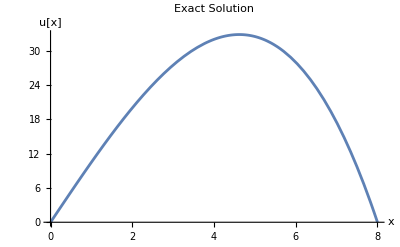

First Derivative: 10.6667-0.5 x^2

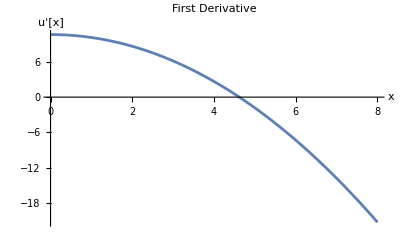

Right-side Function: x

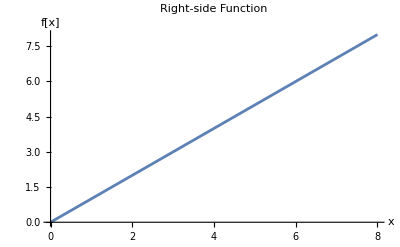

```mathematica
{Uexact, dUexact,fRight} = SolveExact[defineExact, g , True];
```

### Linear Elements

```mathematica
NumberElements = 4;
ExtremeElementsOrder = 1; (*First and last elements*)
InternalElementsOrder = 1;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

f(x)=x

El.1 ksi=-0.774597 x=0.225403 f(x)=0.225403

El.1 ksi=0. x=1. f(x)=1.

El.1 ksi=0.774597 x=1.7746 f(x)=1.7746

Element 1: (0.5 | -0.5
-0.5 | 0.5)(0.666667
1.33333)

El.2 ksi=-0.774597 x=2.2254 f(x)=2.2254

El.2 ksi=0. x=3. f(x)=3.

El.2 ksi=0.774597 x=3.7746 f(x)=3.7746

Element 2: (0.5 | -0.5
-0.5 | 0.5)(2.66667
3.33333)

El.3 ksi=-0.774597 x=4.2254 f(x)=4.2254

El.3 ksi=0. x=5. f(x)=5.

El.3 ksi=0.774597 x=5.7746 f(x)=5.7746

Element 3: (0.5 | -0.5
-0.5 | 0.5)(4.66667
5.33333)

El.4 ksi=-0.774597 x=6.2254 f(x)=6.2254

El.4 ksi=0. x=7. f(x)=7.

El.4 ksi=0.774597 x=7.7746 f(x)=7.7746

Element 4: (0.5 | -0.5
-0.5 | 0.5)(6.66667
7.33333)

Approximation error: 8.86537

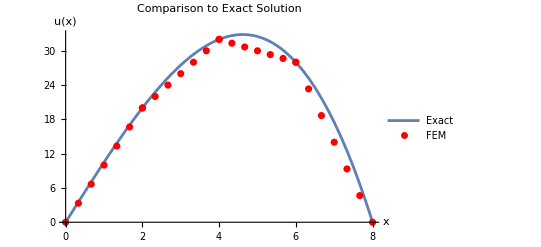

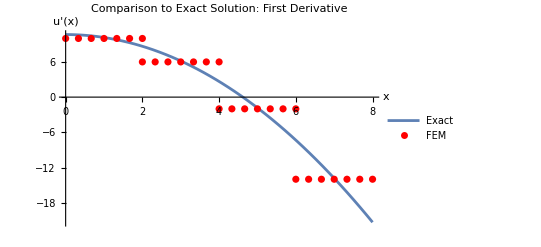

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector, Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem,True];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

```mathematica
Print["Stiffness Matrix: ",MatrixForm[StiffMatrix]];
Print["Force Vector:",MatrixForm[ForceVector]];
Print["Solution:",MatrixForm[Solution]];
```

Stiffness Matrix: (1.×10^12 | -0.5 | 0 | 0 | 0
-0.5 | 1. | -0.5 | 0 | 0
0 | -0.5 | 1. | -0.5 | 0
0 | 0 | -0.5 | 1. | -0.5
0 | 0 | 0 | -0.5 | 1.×10^12)

Force Vector:(0.666667
4.
8.
12.
7.33333)

Solution:(1.06667×10^-11
20.
32.
28.
2.13333×10^-11)

### Quadratic Elements

```mathematica
NumberElements = 8;
ExtremeElementsOrder = 2; (*First and last elements*)
InternalElementsOrder = 2;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

f(x)=x

El.1 ksi=-0.861136 x=0.0694318 f(x)=0.0694318

El.1 ksi=-0.339981 x=0.330009 f(x)=0.330009

El.1 ksi=0.339981 x=0.669991 f(x)=0.669991

El.1 ksi=0.861136 x=0.930568 f(x)=0.930568

Element 1: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(0.166667
0.333333
0.333333)

El.2 ksi=-0.861136 x=1.06943 f(x)=1.06943

El.2 ksi=-0.339981 x=1.33001 f(x)=1.33001

El.2 ksi=0.339981 x=1.66999 f(x)=1.66999

El.2 ksi=0.861136 x=1.93057 f(x)=1.93057

Element 2: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(0.666667
0.833333
1.)

El.3 ksi=-0.861136 x=2.06943 f(x)=2.06943

El.3 ksi=-0.339981 x=2.33001 f(x)=2.33001

El.3 ksi=0.339981 x=2.66999 f(x)=2.66999

El.3 ksi=0.861136 x=2.93057 f(x)=2.93057

Element 3: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(1.16667
1.33333
1.66667)

El.4 ksi=-0.861136 x=3.06943 f(x)=3.06943

El.4 ksi=-0.339981 x=3.33001 f(x)=3.33001

El.4 ksi=0.339981 x=3.66999 f(x)=3.66999

El.4 ksi=0.861136 x=3.93057 f(x)=3.93057

Element 4: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(1.66667
1.83333
2.33333)

El.5 ksi=-0.861136 x=4.06943 f(x)=4.06943

El.5 ksi=-0.339981 x=4.33001 f(x)=4.33001

El.5 ksi=0.339981 x=4.66999 f(x)=4.66999

El.5 ksi=0.861136 x=4.93057 f(x)=4.93057

Element 5: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(2.16667
2.33333
3.)

El.6 ksi=-0.861136 x=5.06943 f(x)=5.06943

El.6 ksi=-0.339981 x=5.33001 f(x)=5.33001

El.6 ksi=0.339981 x=5.66999 f(x)=5.66999

El.6 ksi=0.861136 x=5.93057 f(x)=5.93057

Element 6: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(2.66667
2.83333
3.66667)

El.7 ksi=-0.861136 x=6.06943 f(x)=6.06943

El.7 ksi=-0.339981 x=6.33001 f(x)=6.33001

El.7 ksi=0.339981 x=6.66999 f(x)=6.66999

El.7 ksi=0.861136 x=6.93057 f(x)=6.93057

Element 7: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(3.16667
3.33333
4.33333)

El.8 ksi=-0.861136 x=7.06943 f(x)=7.06943

El.8 ksi=-0.339981 x=7.33001 f(x)=7.33001

El.8 ksi=0.339981 x=7.66999 f(x)=7.66999

El.8 ksi=0.861136 x=7.93057 f(x)=7.93057

Element 8: (1. | -1. | 0.
-1. | 1. | 0.
0. | 0. | 5.33333)(3.66667
3.83333
5.)

Approximation error: 0.106657

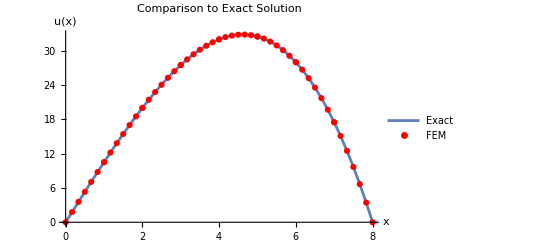

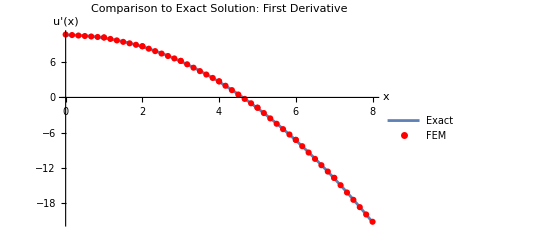

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector,Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem,True];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

```mathematica
Print["Stiffness Matrix: ",MatrixForm[StiffMatrix]];
Print["Force Vector:",MatrixForm[ForceVector]];
Print["Solution:",MatrixForm[Solution]];
```

Stiffness Matrix: (1.×10^12 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1.×10^12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.
0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33333)

Force Vector:(0.166667
1.
2.
3.
4.
5.
6.
7.
3.83333
0.333333
1.
1.66667
2.33333
3.
3.66667
4.33333
5.)

Solution:(1.06667×10^-11
10.5
20.
27.5
32.
32.5
28.
17.5
2.13333×10^-11
0.0625
0.1875
0.3125
0.4375
0.5625
0.6875
0.8125
0.9375)

### Error Function Analysis

```mathematica
NumberElementsMin = 4;
NumberElementsMax = 128;
```

Convergence exponent with elements of order 1: 1.00204

Convergence exponent with elements of order 2: 2.0005

Convergence exponent with elements of order 3: -0.0644349

Convergence exponent with elements of order 4: -0.0601708

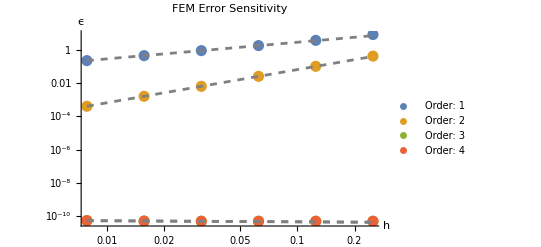

```mathematica
ErrorsStandard=FEMErrorAnalysis[Uexact, dUexact, defineExact, g,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax,1, 4];
FEMErrorAnalysisPlot[ErrorsStandard,1]
```

## “Pulse” Problem

### “Right-side” Function

```mathematica
defineExact = True; (*True => g(x) == u(x); False => g(x) == -u'' + u == f(x) *)
eps = E^(-1);
g[x_]:= E^(-(x-h/2)^2/eps)-E^(-(h/2)^2/eps);
```

Problem:

0.-u''=-2 ⅇ^(1-ⅇ (-4+x)^2) (-1+2 ⅇ (-4+x)^2)

1. u(0)+0.=0.

1. u(8)+0.=0.

Exact Solution: (ⅇ^(-ⅇ (x-4)^2)-1.29254×10^-19)(x)

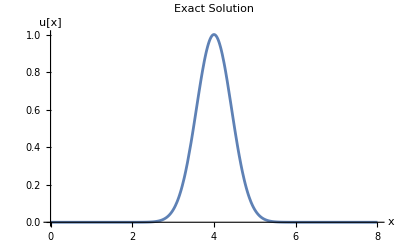

First Derivative: -2 ⅇ^(1-ⅇ (x-4)^2) (x-4)

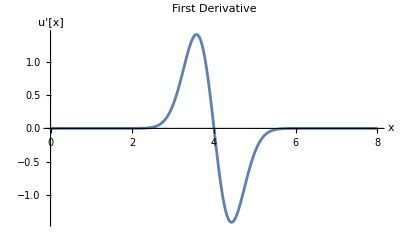

Right-side Function: -2 ⅇ^(1-ⅇ (x-4)^2) (2 ⅇ (x-4)^2-1)

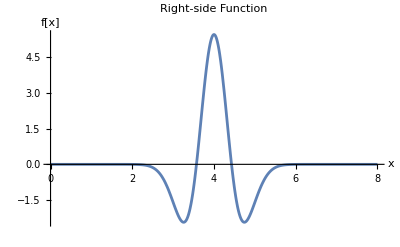

```mathematica
{Uexact, dUexact,fRight} = SolveExact[defineExact, g , True];
```

```mathematica
NumberElements = 8;
ExtremeElementsOrder = 1; (*First and last elements*)
InternalElementsOrder = 1;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

f(x)=-2 ⅇ^(1-ⅇ (x-4)^2) (2 ⅇ (x-4)^2-1)

El.1 ksi=-0.774597 x=0.112702 f(x)=-6.3894×10^-16

El.1 ksi=0. x=0.5 f(x)=-1.23215×10^-12

El.1 ksi=0.774597 x=0.887298 f(x)=-1.02448×10^-9

Element 1: (1. | -1.
-1. | 1.)(-3.23463×10^-11
-2.52779×10^-10)

El.2 ksi=-0.774597 x=1.1127 f(x)=-3.47076×10^-8

El.2 ksi=0. x=1.5 f(x)=-7.50262×10^-6

El.2 ksi=0.774597 x=1.8873 f(x)=-0.000680334

Element 2: (1. | -1.
-1. | 1.)(-0.0000229743
-0.000169351)

El.3 ksi=-0.774597 x=2.1127 f(x)=-0.00622819

El.3 ksi=0. x=2.5 f(x)=-0.134769

El.3 ksi=0.774597 x=2.8873 f(x)=-1.0763

Element 3: (1. | -1.
-1. | 1.)(-0.0651782
-0.29542)

El.4 ksi=-0.774597 x=3.1127 f(x)=-2.09793

El.4 ksi=0. x=3.5 f(x)=-0.989591

El.4 ksi=0.774597 x=3.8873 f(x)=4.88939

Element 4: (1. | -1.
-1. | 1.)(-0.583923
0.919509)

El.5 ksi=-0.774597 x=4.1127 f(x)=4.88939

El.5 ksi=0. x=4.5 f(x)=-0.989591

El.5 ksi=0.774597 x=4.8873 f(x)=-2.09793

Element 5: (1. | -1.
-1. | 1.)(0.919509
-0.583923)

El.6 ksi=-0.774597 x=5.1127 f(x)=-1.0763

El.6 ksi=0. x=5.5 f(x)=-0.134769

El.6 ksi=0.774597 x=5.8873 f(x)=-0.00622819

Element 6: (1. | -1.
-1. | 1.)(-0.29542
-0.0651782)

El.7 ksi=-0.774597 x=6.1127 f(x)=-0.000680334

El.7 ksi=0. x=6.5 f(x)=-7.50262×10^-6

El.7 ksi=0.774597 x=6.8873 f(x)=-3.47076×10^-8

Element 7: (1. | -1.
-1. | 1.)(-0.000169351
-0.0000229743)

El.8 ksi=-0.774597 x=7.1127 f(x)=-1.02448×10^-9

El.8 ksi=0. x=7.5 f(x)=-1.23215×10^-12

El.8 ksi=0.774597 x=7.8873 f(x)=-6.3894×10^-16

Element 8: (1. | -1.
-1. | 1.)(-2.52779×10^-10
-3.23463×10^-11)

Approximation error: 0.586524

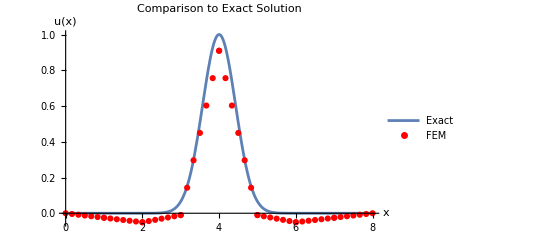

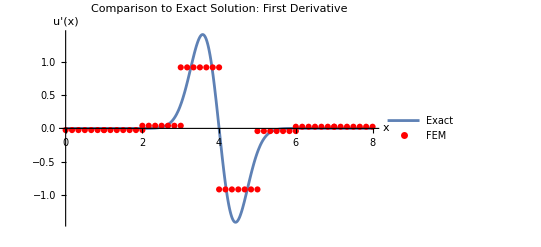

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector,Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem,True];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

```mathematica
Print["Stiffness Matrix: ",MatrixForm[StiffMatrix]];
Print["Force Vector:",MatrixForm[ForceVector]];
Print["Solution:",MatrixForm[Solution]];
```

Stiffness Matrix: (1.×10^12 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1. | 2. | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 2. | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 2. | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 2. | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 2. | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 2. | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 2. | -1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1.×10^12)

Force Vector:(-3.23463×10^-11
-0.0000229746
-0.0653475
-0.879343
1.83902
-0.879343
-0.0653475
-0.0000229746
-3.23463×10^-11)

Solution:(-2.52043×10^-14
-0.0252043
-0.0503856
-0.0102194
0.90929
-0.0102194
-0.0503856
-0.0252043
-2.52043×10^-14)

Convergence exponent with elements of order 1: 0.992584

Convergence exponent with elements of order 2: 1.98906

Convergence exponent with elements of order 3: 2.98796

Convergence exponent with elements of order 4: 3.9874

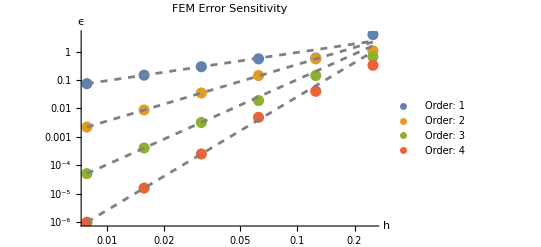

```mathematica
ErrorsStandard=FEMErrorAnalysis[Uexact, dUexact, defineExact, g,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax,1, 4];
FEMErrorAnalysisPlot[ErrorsStandard,1]
```